https://en.wikipedia.org/wiki/Fabry%E2%80%93P%C3%A9rot_interferometer

```mathematica
CFinConv=Function[fin,1/(Sin[π/(2 fin)])^2];
N[coeffin[200]]
FPTrans=Function[{cfin,δ},1/(1+cfin (Sin[δ])^2)];
```

16211.7

```mathematica
fineval=200;
```

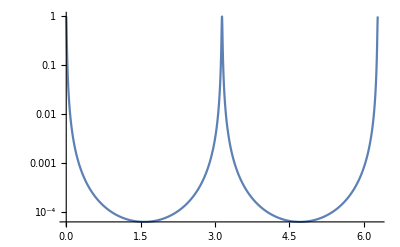

```mathematica
LogPlot[FPTrans[CFinConv[fineval],x],{x,0,2π},PlotRange->All]
```

```mathematica
peakδ=1.*π/fineval;
Ppeak=NIntegrate[FPTrans[CFinConv[fineval],x],{x,-peakδ,peakδ}]
Pback=NIntegrate[FPTrans[CFinConv[fineval],x],{x,peakδ,π-peakδ}]
Pback/Ppeak
```

0.0173911

0.00728189

0.418713

```mathematica
PRatioWidths=Function[{fin,widths},Module[{locpeakδ},
locpeakδ=widths*π/fineval; (*max value  ~0.25/(π/fineval) *)
Ppeak=NIntegrate[FPTrans[CFinConv[fin],x],{x,-locpeakδ,locpeakδ}];
Pback=NIntegrate[FPTrans[CFinConv[fin],x],{x,locpeakδ,π-locpeakδ}];
Pback/Ppeak]]
```

Function[{fin,widths},Module[{locpeakδ},locpeakδ=(widths π)/fineval;Ppeak=NIntegrate[FPTrans[CFinConv[fin],x],{x,-locpeakδ,locpeakδ}];Pback=NIntegrate[FPTrans[CFinConv[fin],x],{x,locpeakδ,π-locpeakδ}];Pback/Ppeak]]

0.0212608

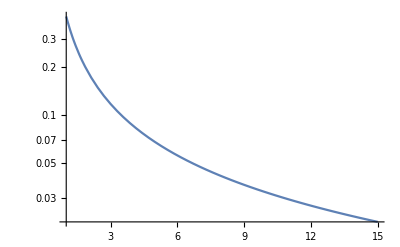

```mathematica
PRatioWidths[200,15]
LogPlot[PRatioWidths[200,x],{x,1,15}]
```

```mathematica
0.25/(π/200.)
```

15.9155